```mathematica
ineqs=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

127

```mathematica
countDone=0;MyLeafCount[exp_]:=Block[{},countDone++;StringLength[ToString[exp]]]
```

```mathematica
ineqsW=Monitor[Simplify[Fold[And,ineqs],Trig->False,ComplexityFunction->MyLeafCount,Assumptions->nullAtomFacts],countDone];Length[ineqsW]
```

127

```mathematica
Length[ineqsW]
```

127

```mathematica
vars=ListofVars[Select[ineqsW,Length[ListofVars[#]]==2&]]
```

{n1234,n123x4,n1234,n124x3,n1234,n12x34,n1234,n134x2,n1234,n13x24,n1234,n14x23,n1234,n1x234,n123x4,n12x3x4,n123x4,n13x2x4,n123x4,n1x23x4,n124x3,n12x3x4,n124x3,n14x2x3,n124x3,n1x24x3,n12x34,n12x3x4,n12x34,n1x2x34,n12x3x4,n1x2x3x4,n134x2,n13x2x4,n134x2,n14x2x3,n134x2,n1x2x34,n13x24,n13x2x4,n13x24,n1x24x3,n13x2x4,n1x2x3x4,n14x23,n14x2x3,n14x23,n1x23x4,n14x2x3,n1x2x3x4,n1x234,n1x23x4,n1x234,n1x24x3,n1x234,n1x2x34,n1x23x4,n1x2x3x4,n1x24x3,n1x2x3x4,n1x2x34,n1x2x3x4}

```mathematica
ineqs2=Table[allGraphs[k,"comp"][allGraphs[k,"colofourrealnull"],0],{k,Keys[allGraphs]}];Length[ineqs]
```

127

```mathematica
ineqs2
```

{n1x2x3x4>0,-n12x3x4+n1x2x3x4>0,n123x4-n12x3x4-n13x2x4+n1x2x3x4>0,-n1234+n123x4+n124x3-n12x3x4+n134x2-n13x2x4-n14x2x3+n1x2x3x4>0,-2 n1234+2 n123x4+n124x3-n12x3x4+n134x2-n13x2x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4>0,-4 n1234+2 n123x4+2 n124x3-n12x3x4+n134x2+n13x24-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-6 n1234+2 n123x4+2 n124x3+n12x34-n12x3x4+2 n134x2+n13x24-n13x2x4+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4≥0,2 n1234-n12x34-n134x2-n1x234+n1x2x34>0,2 n1234-n124x3-n13x24-n1x234+n1x24x3≥0,-4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,n1234-n123x4-n14x23+n1x23x4>0,2 n1234-n123x4-n14x23-n1x234+n1x23x4>0,-n1234+n1x234>0,-2 n1234+n123x4+2 n124x3-n12x3x4+n134x2+n13x24-n13x2x4-n14x2x3-n1x24x3+n1x2x3x4>0,-4 n1234+n123x4+2 n124x3+n12x34-n12x3x4+2 n134x2+n13x24-n13x2x4-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,n1234-n124x3-n13x24+n1x24x3>0,-2 n1234+n123x4+n124x3+n12x34-n12x3x4+2 n134x2-n13x2x4-n14x2x3-n1x2x34+n1x2x3x4>0,n1234-n12x34-n134x2+n1x2x34>0,n1234-n124x3-n134x2+n14x2x3>0,2 n1234-n124x3-n134x2-n14x23+n14x2x3>0,-n1234+n14x23>0,2 n123x4-n12x3x4-n13x2x4-n1x23x4+n1x2x3x4>0,-2 n1234+2 n123x4+n124x3-n12x3x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-4 n1234+2 n123x4+n124x3+n12x34-n12x3x4+n134x2+n13x24-n13x2x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,-2 n1234+2 n123x4+n12x34-n12x3x4+n134x2-n13x2x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,-n123x4+n1x23x4>0,n1234-n123x4-n1x234+n1x23x4>0,-n1234+n123x4+n124x3-n12x3x4+n13x24-n13x2x4-n1x24x3+n1x2x3x4>0,-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n13x24-n13x2x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,-n1234+n123x4+n12x34-n12x3x4+n134x2-n13x2x4-n1x2x34+n1x2x3x4>0,-n123x4+n13x2x4>0,n1234-n123x4-n134x2+n13x2x4>0,2 n1234-n123x4-n134x2-n13x24+n13x2x4≥0,-n1234+n13x24≥0,-n1234+n134x2>0,n1234-n123x4-n13x24+n13x2x4>0,n124x3-n12x3x4-n14x2x3+n1x2x3x4>0,-n1234+n123x4+n124x3-n12x3x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4>0,-2 n1234+n123x4+2 n124x3-n12x3x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-4 n1234+n123x4+2 n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,n1234-n124x3-n1x234+n1x24x3>0,-3 n1234+n123x4+n124x3+n12x34-n12x3x4+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,2 n124x3-n12x3x4-n14x2x3-n1x24x3+n1x2x3x4>0,-2 n1234+2 n124x3+n12x34-n12x3x4+n134x2-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,-n124x3+n1x24x3>0,-n1234+n124x3+n12x34-n12x3x4+n134x2-n14x2x3-n1x2x34+n1x2x3x4>0,-n124x3+n14x2x3>0,n1234-n124x3-n14x23+n14x2x3>0,n123x4-n12x3x4-n1x23x4+n1x2x3x4>0,-n1234+n123x4+n124x3-n12x3x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-2 n1234+n123x4+n124x3+n12x34-n12x3x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,n1234-n12x34-n1x234+n1x2x34>0,-n1234+n123x4+n12x34-n12x3x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,n124x3-n12x3x4-n1x24x3+n1x2x3x4>0,-n1234+n124x3+n12x34-n12x3x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,n12x34-n12x3x4-n1x2x34+n1x2x3x4>0,-n12x34+n1x2x34>0,n12x3x4>0,-n123x4+n12x3x4>0,n1234-n123x4-n124x3+n12x3x4>0,2 n1234-n123x4-n124x3-n12x34+n12x3x4>0,-n1234+n12x34>0,-n1234+n124x3>0,n1234-n123x4-n12x34+n12x3x4>0,n123x4>0,-n1234+n123x4>0,n1234>0,-n124x3+n12x3x4>0,n1234-n124x3-n12x34+n12x3x4>0,n124x3>0,-n12x34+n12x3x4>0,n12x34>0,-n13x2x4+n1x2x3x4>0,n134x2-n13x2x4-n14x2x3+n1x2x3x4>0,-n1234+n123x4+n134x2-n13x2x4+n14x23-n14x2x3-n1x23x4+n1x2x3x4>0,-3 n1234+n123x4+n124x3+n134x2+n13x24-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-4 n1234+n123x4+n124x3+2 n134x2+n13x24-n13x2x4+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,n1234-n134x2-n1x234+n1x2x34>0,-2 n1234+n123x4+2 n134x2-n13x2x4+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,-n1234+n124x3+n134x2+n13x24-n13x2x4-n14x2x3-n1x24x3+n1x2x3x4>0,-2 n1234+n124x3+2 n134x2+n13x24-n13x2x4-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,2 n134x2-n13x2x4-n14x2x3-n1x2x34+n1x2x3x4>0,-n134x2+n1x2x34>0,-n134x2+n14x2x3>0,n1234-n134x2-n14x23+n14x2x3>0,n123x4-n13x2x4-n1x23x4+n1x2x3x4>0,-n1234+n123x4+n13x24-n13x2x4+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-2 n1234+n123x4+n134x2+n13x24-n13x2x4+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,n1234-n13x24-n1x234+n1x24x3>0,-n1234+n123x4+n134x2-n13x2x4+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,n13x24-n13x2x4-n1x24x3+n1x2x3x4>0,-n1234+n134x2+n13x24-n13x2x4+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,-n13x24+n1x24x3>0,n134x2-n13x2x4-n1x2x34+n1x2x3x4>0,n13x2x4>0,-n134x2+n13x2x4>0,n1234-n134x2-n13x24+n13x2x4>0,n134x2>0,-n13x24+n13x2x4>0,n13x24>0,-n14x2x3+n1x2x3x4>0,n14x23-n14x2x3-n1x23x4+n1x2x3x4>0,-n1234+n124x3+n14x23-n14x2x3+n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,-2 n1234+n124x3+n134x2+n14x23-n14x2x3+2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,-n1234+n134x2+n14x23-n14x2x3+n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,-n14x23+n1x23x4>0,n1234-n14x23-n1x234+n1x23x4>0,n124x3-n14x2x3-n1x24x3+n1x2x3x4>0,-n1234+n124x3+n134x2-n14x2x3+n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,n134x2-n14x2x3-n1x2x34+n1x2x3x4>0,n14x2x3>0,-n14x23+n14x2x3>0,n14x23>0,-n1x23x4+n1x2x3x4>0,n1x234-n1x23x4-n1x24x3+n1x2x3x4>0,2 n1x234-n1x23x4-n1x24x3-n1x2x34+n1x2x3x4>0,-n1x234+n1x2x34>0,-n1x234+n1x24x3>0,n1x234-n1x23x4-n1x2x34+n1x2x3x4>0,n1x23x4>0,-n1x234+n1x23x4>0,n1x234>0,-n1x24x3+n1x2x3x4>0,n1x234-n1x24x3-n1x2x34+n1x2x3x4>0,n1x24x3>0,-n1x2x34+n1x2x3x4>0,n1x2x34>0}

```mathematica
realnullAtomFacts=Table[allGraphs[k]["comp"][allGraphs[k]["colofourrealnull"],0],{k,realyNullAtomKeys}];Length[realnullAtomFacts]
```

15

```mathematica
ineqsW2=Monitor[Simplify[Fold[And,ineqs2],Trig->False,ComplexityFunction->MyLeafCount],countDone];Length[ineqsW2]
```

127

```mathematica
Length[allGraphs]
```

127

```mathematica
Table[Labeled[allGraphs[k,"graph"],k],{k,Keys[allGraphs]}]
```

{-Graphics-0,-Graphics-243,-Graphics-324,-Graphics-351,-Graphics-360,-Graphics-363,-Graphics-364,-Graphics-365,-Graphics-367,-Graphics-361,-Graphics-369,-Graphics-373,-Graphics-377,-Graphics-354,-Graphics-355,-Graphics-357,-Graphics-352,-Graphics-353,-Graphics-382,-Graphics-391,-Graphics-400,-Graphics-333,-Graphics-336,-Graphics-337,-Graphics-334,-Graphics-342,-Graphics-346,-Graphics-327,-Graphics-328,-Graphics-325,-Graphics-414,-Graphics-442,-Graphics-445,-Graphics-448,-Graphics-473,-Graphics-417,-Graphics-270,-Graphics-279,-Graphics-282,-Graphics-283,-Graphics-286,-Graphics-280,-Graphics-273,-Graphics-274,-Graphics-276,-Graphics-271,-Graphics-300,-Graphics-309,-Graphics-252,-Graphics-255,-Graphics-256,-Graphics-257,-Graphics-253,-Graphics-246,-Graphics-247,-Graphics-244,-Graphics-245,-Graphics-486,-Graphics-576,-Graphics-606,-Graphics-607,-Graphics-608,-Graphics-637,-Graphics-577,-Graphics-666,-Graphics-697,-Graphics-728,-Graphics-516,-Graphics-517,-Graphics-546,-Graphics-487,-Graphics-488,-Graphics-81,-Graphics-108,-Graphics-117,-Graphics-120,-Graphics-121,-Graphics-122,-Graphics-118,-Graphics-111,-Graphics-112,-Graphics-109,-Graphics-110,-Graphics-136,-Graphics-145,-Graphics-90,-Graphics-93,-Graphics-94,-Graphics-97,-Graphics-91,-Graphics-84,-Graphics-85,-Graphics-87,-Graphics-82,-Graphics-162,-Graphics-190,-Graphics-193,-Graphics-218,-Graphics-165,-Graphics-168,-Graphics-27,-Graphics-36,-Graphics-39,-Graphics-40,-Graphics-37,-Graphics-45,-Graphics-49,-Graphics-30,-Graphics-31,-Graphics-28,-Graphics-54,-Graphics-63,-Graphics-72,-Graphics-9,-Graphics-12,-Graphics-13,-Graphics-14,-Graphics-16,-Graphics-10,-Graphics-18,-Graphics-22,-Graphics-26,-Graphics-3,-Graphics-4,-Graphics-6,-Graphics-1,-Graphics-2}

```mathematica
allGraphs[9,"colofourrealnull"]
```

-n1x23x4+n1x2x3x4

```mathematica
Select[ineqsW2,Elemen
```

```mathematica
vars2=ListofVars[Select[ineqsW2,Length[ListofVars[#]]==2&]]
```

{n1234,n123x4,n1234,n124x3,n1234,n12x34,n1234,n134x2,n1234,n13x24,n1234,n14x23,n1234,n1x234,n123x4,n12x3x4,n123x4,n13x2x4,n123x4,n1x23x4,n124x3,n12x3x4,n124x3,n14x2x3,n124x3,n1x24x3,n12x34,n12x3x4,n12x34,n1x2x34,n12x3x4,n1x2x3x4,n134x2,n13x2x4,n134x2,n14x2x3,n134x2,n1x2x34,n13x24,n13x2x4,n13x24,n1x24x3,n13x2x4,n1x2x3x4,n14x23,n14x2x3,n14x23,n1x23x4,n14x2x3,n1x2x3x4,n1x234,n1x23x4,n1x234,n1x24x3,n1x234,n1x2x34,n1x23x4,n1x2x3x4,n1x24x3,n1x2x3x4,n1x2x34,n1x2x3x4}

```mathematica
InverseNull[symbol_]:=First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==symbol&]]
```

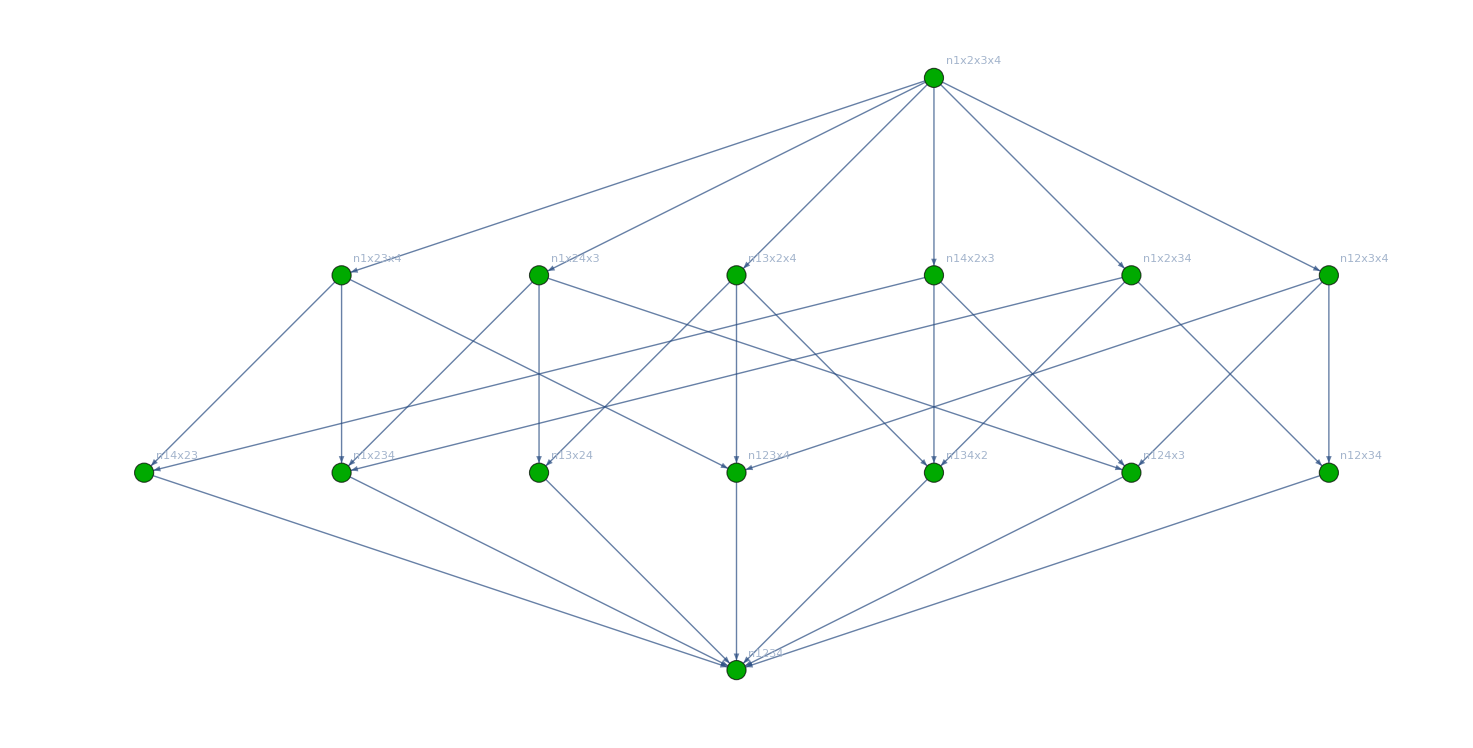

```mathematica
partialOrder=Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[k->Labeled[allGraphs[InverseNull[k],"graph"],k],{k,vars2}],GraphLayout->"LayeredDigraphEmbedding", VertexStyle->Table[k->ColourForKey[allGraphs,InverseNull[k]],{k,vars2}]]
```

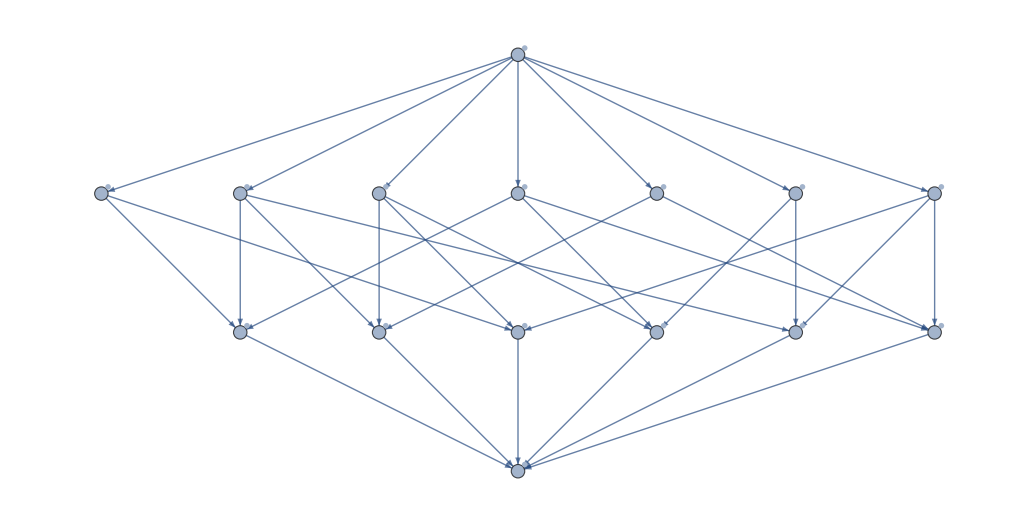

```mathematica
Graph[Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofourrealnull"]->allGraphs[k,"graph"],{k,realyNullAtomKeys}],MemberQ[vars2,#[[1]]]&]]
```

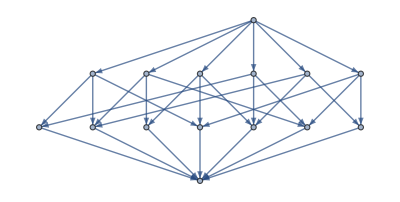

```mathematica
Graph[Map[#[[1]]->#[[2]]&,AndToTable[Select[ineqsW,Length[ListofVars[#]]==2&]]],VertexLabels->Select[Table[allGraphs[k,"colofournull"]->allGraphs[k,"graph"],{k,nullAtomKeys}],MemberQ[vars,#[[1]]]&]]
```

```mathematica
Take[ineqsW,5]
```

n1x2x3x4>0&&n1x2x3x4>n12x3x4&&n123x4+n1x2x3x4>n12x3x4+n13x2x4&&n123x4+n124x3+n134x2+n1x2x3x4>n1234+n12x3x4+n13x2x4+n14x2x3&&2 n123x4+n124x3+n134x2+n14x23+n1x2x3x4>2 n1234+n12x3x4+n13x2x4+n14x2x3+n1x23x4

```mathematica
pairs=Subsets[nullAtomSymbols,{2}];Length[pairs]
```

105

```mathematica
Take[nullAtomFacts,3]
```

{p1x2x3x4>0,p1x2x34>0,p1x24x3>0}

```mathematica
atomFactsAnd=Fold[And,nullAtomFacts]
```

p1x2x3x4>0&&p1x2x34>0&&p1x24x3>0&&p1x23x4>0&&p1x234>0&&p14x2x3>0&&p14x23>0&&p13x2x4>0&&p13x24>0&&p134x2>0&&p12x3x4>0&&p12x34>0&&p124x3>0&&p123x4>0&&p1234≥0

```mathematica
Monitor[Table[{p[[1]]<p[[2]]}->Length[Simplify[p[[1]]>p[[2]]&&atomFactsAnd,Trig->False,ComplexityFunction->MyLeafCount,Assumptions->nullAtomFacts]],{p,pairs}],Position[pairs, p]]
```

{{p1x2x3x4<p1x2x34}→2,{p1x2x3x4<p1x24x3}→2,{p1x2x3x4<p1x23x4}→2,{p1x2x3x4<p1x234}→2,{p1x2x3x4<p14x2x3}→2,{p1x2x3x4<p14x23}→2,{p1x2x3x4<p13x2x4}→2,{p1x2x3x4<p13x24}→2,{p1x2x3x4<p134x2}→2,{p1x2x3x4<p12x3x4}→2,{p1x2x3x4<p12x34}→2,{p1x2x3x4<p124x3}→2,{p1x2x3x4<p123x4}→2,{p1x2x3x4<p1234}→2,{p1x2x34<p1x24x3}→2,{p1x2x34<p1x23x4}→2,{p1x2x34<p1x234}→2,{p1x2x34<p14x2x3}→2,{p1x2x34<p14x23}→2,{p1x2x34<p13x2x4}→2,{p1x2x34<p13x24}→2,{p1x2x34<p134x2}→2,{p1x2x34<p12x3x4}→2,{p1x2x34<p12x34}→2,{p1x2x34<p124x3}→2,{p1x2x34<p123x4}→2,{p1x2x34<p1234}→2,{p1x24x3<p1x23x4}→2,{p1x24x3<p1x234}→2,{p1x24x3<p14x2x3}→2,{p1x24x3<p14x23}→2,{p1x24x3<p13x2x4}→2,{p1x24x3<p13x24}→2,{p1x24x3<p134x2}→2,{p1x24x3<p12x3x4}→2,{p1x24x3<p12x34}→2,{p1x24x3<p124x3}→2,{p1x24x3<p123x4}→2,{p1x24x3<p1234}→2,{p1x23x4<p1x234}→2,{p1x23x4<p14x2x3}→2,{p1x23x4<p14x23}→2,{p1x23x4<p13x2x4}→2,{p1x23x4<p13x24}→2,{p1x23x4<p134x2}→2,{p1x23x4<p12x3x4}→2,{p1x23x4<p12x34}→2,{p1x23x4<p124x3}→2,{p1x23x4<p123x4}→2,{p1x23x4<p1234}→2,{p1x234<p14x2x3}→2,{p1x234<p14x23}→2,{p1x234<p13x2x4}→2,{p1x234<p13x24}→2,{p1x234<p134x2}→2,{p1x234<p12x3x4}→2,{p1x234<p12x34}→2,{p1x234<p124x3}→2,{p1x234<p123x4}→2,{p1x234<p1234}→2,{p14x2x3<p14x23}→2,{p14x2x3<p13x2x4}→2,{p14x2x3<p13x24}→2,{p14x2x3<p134x2}→2,{p14x2x3<p12x3x4}→2,{p14x2x3<p12x34}→2,{p14x2x3<p124x3}→2,{p14x2x3<p123x4}→2,{p14x2x3<p1234}→2,{p14x23<p13x2x4}→2,{p14x23<p13x24}→2,{p14x23<p134x2}→2,{p14x23<p12x3x4}→2,{p14x23<p12x34}→2,{p14x23<p124x3}→2,{p14x23<p123x4}→2,{p14x23<p1234}→2,{p13x2x4<p13x24}→2,{p13x2x4<p134x2}→2,{p13x2x4<p12x3x4}→2,{p13x2x4<p12x34}→2,{p13x2x4<p124x3}→2,{p13x2x4<p123x4}→2,{p13x2x4<p1234}→2,{p13x24<p134x2}→2,{p13x24<p12x3x4}→2,{p13x24<p12x34}→2,{p13x24<p124x3}→2,{p13x24<p123x4}→2,{p13x24<p1234}→2,{p134x2<p12x3x4}→2,{p134x2<p12x34}→2,{p134x2<p124x3}→2,{p134x2<p123x4}→2,{p134x2<p1234}→2,{p12x3x4<p12x34}→2,{p12x3x4<p124x3}→2,{p12x3x4<p123x4}→2,{p12x3x4<p1234}→2,{p12x34<p124x3}→2,{p12x34<p123x4}→2,{p12x34<p1234}→2,{p124x3<p123x4}→2,{p124x3<p1234}→2,{p123x4<p1234}→2}

```mathematica
Select[nullAtomSymbols,!MemberQ[ListofVars[ Table[allGraphs[k,"colofournull"],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]//Total//Expand],#]&]
```

{p1x2x3x4,p1x2x34,p1x24x3,p1x23x4,p1x234,p14x2x3,p14x23,p13x2x4,p13x24,p134x2,p12x3x4,p12x34,p124x3,p123x4,p1234}

```mathematica
Select[Keys[allGraphs],allGraphs[#,"colofournull"]==p1x2x3x4x5&]
```

{}

```mathematica
allGraphs[0,"graph"]
```

-Graphics-

```mathematica
allGraphs[quad1Key,"colofournull"]/.repcolofournullgraph2//Expand//Length
```

2

```mathematica
Select[nullAtomSymbols,!MemberQ[ListofVars[ Table[allGraphs[k,"colofournull"],{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]//Total//Expand],#]&]
```

{p1x2x3x4,p1x2x34,p1x24x3,p1x23x4,p1x234,p14x2x3,p14x23,p13x2x4,p13x24,p134x2,p12x3x4,p12x34,p124x3,p123x4,p1234}

```mathematica
Select[Keys[allGraphs],MemberQ[{p1x2x3x4x5,p1x25x34,p15x24x3,p14x23x5,p13x2x45,p12x35x4},allGraphs[#,"colofournull"]]&]
```

{}

```mathematica
allGraphs[6562,"graph"]
```

Missing[KeyAbsent,6562]

## Mobius and zeta

```mathematica
Sort[Map[First,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]]]
```

{n123x4,n124x3,n12x34,n12x3x4,n12x3x4,n12x3x4,n134x2,n13x24,n13x2x4,n13x2x4,n13x2x4,n14x23,n14x2x3,n14x2x3,n14x2x3,n1x234,n1x23x4,n1x23x4,n1x23x4,n1x24x3,n1x24x3,n1x24x3,n1x2x34,n1x2x34,n1x2x34,n1x2x3x4,n1x2x3x4,n1x2x3x4,n1x2x3x4,n1x2x3x4,n1x2x3x4}

```mathematica
Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofourrealnull"]]]==15&]
```

{364}

```mathematica
vertices=Sort[Sort[ListofVars[allGraphs[364,"colofourrealnull"]]],StringCount [SymbolName[#1],"x"]<StringCount [SymbolName[#2],"x"]&]
```

{n1234,n1x234,n14x23,n13x24,n134x2,n12x34,n124x3,n123x4,n1x2x34,n1x24x3,n1x23x4,n14x2x3,n13x2x4,n12x3x4,n1x2x3x4}

```mathematica
Length[vertices]
```

15

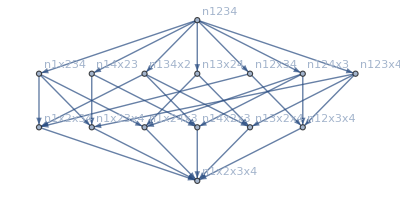

```mathematica
four=Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->"Name",GraphLayout->"LayeredDigraphEmbedding"]
```

```mathematica
ChromaticPolynomial[CompleteGraph[4],x]
```

-6 x+11 x^2-6 x^3+x^4

```mathematica
IM=IdentityMatrix[Length[VertexList[four]]];
```

```mathematica
fourM=AdjacencyMatrix[four];MatrixForm[fourM]
```

(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MakeOne[mat_]:=Map[Map[If[#>0,1,0]&,#]&, mat]
```

```mathematica
ZetaM=MakeOne[Inverse[IM-fourM]];MatrixForm[ZetaM]
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
MobiusM=Inverse[ZetaM];MatrixForm[MobiusM,TableHeadings->{VertexList[four], VertexList[four]}]
```

( | n1234 | n1x234 | n14x23 | n13x24 | n134x2 | n12x34 | n124x3 | n123x4 | n1x2x34 | n1x24x3 | n1x23x4 | n14x2x3 | n13x2x4 | n12x3x4 | n1x2x3x4
n1234 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 2 | 2 | 2 | 2 | 2 | 2 | -6
n1x234 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | 0 | 0 | 0 | 2
n14x23 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 1
n13x24 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 1
n134x2 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 2
n12x34 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 1
n124x3 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 2
n123x4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1 | 0 | -1 | -1 | 2
n1x2x34 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1
n1x24x3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
n1x23x4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -1
n14x2x3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
n13x2x4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
n12x3x4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
n1x2x3x4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Det[MobiusM]
```

1

```mathematica
Mob=Association[]
```

<||>

```mathematica
With[{l=VertexList[four]},
Table[Mob[l[[k]]]=MobiusM[[k,Length[l]]],{k,1,Length[l]}]
]
```

{-6,2,1,1,2,1,2,2,-1,-1,-1,-1,-1,-1,1}

```mathematica
Gr=Association[];With[{l=VertexList[four]},
Table[Gr[l[[k]]]=allGraphs[First[Select[Keys[allGraphs],allGraphs[#,"colofourrealnull"]==l[[k]]&]],"vertexsets"],{k,1,Length[l]}]
]
```

{{{1},{2},{3},{4}},{{1},{2},{3,4}},{{1},{2,4},{3}},{{1},{2,3},{4}},{{1,4},{2},{3}},{{1,3},{2},{4}},{{1,2},{3},{4}},{{1},{2,3,4}},{{1,4},{2,3}},{{1,3},{2,4}},{{1,3,4},{2}},{{1,2},{3,4}},{{1,2,4},{3}},{{1,2,3},{4}},{{1,2,3,4}}}

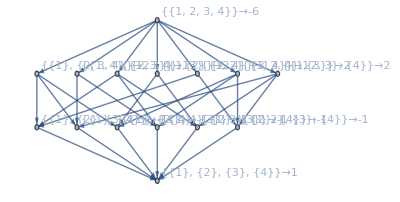

```mathematica
Graph[vertices,Map[#[[2]]->#[[1]]&,AndToTable[Select[ineqsW2,Length[ListofVars[#]]==2&]]],VertexLabels->Table[v->Rotate[ToString[Gr[v]],Pi/4]->Mob[v],{v,VertexList[four]}],GraphLayout->"LayeredDigraphEmbedding"]
```

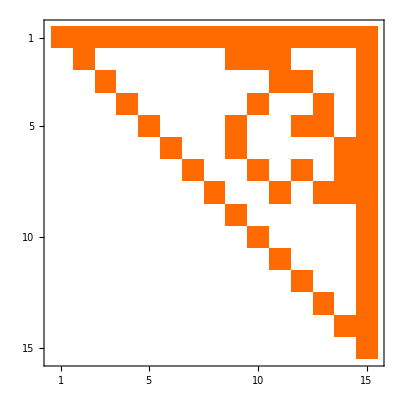

```mathematica
ZetaM//MatrixPlot
```

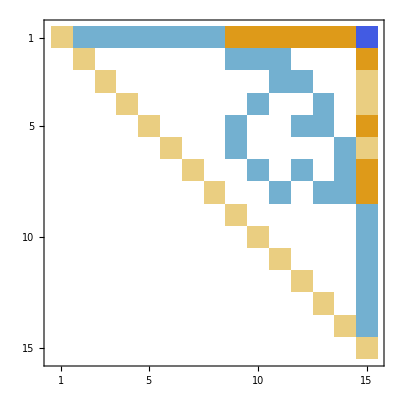

```mathematica
Inverse[ZetaM]//MatrixPlot
```

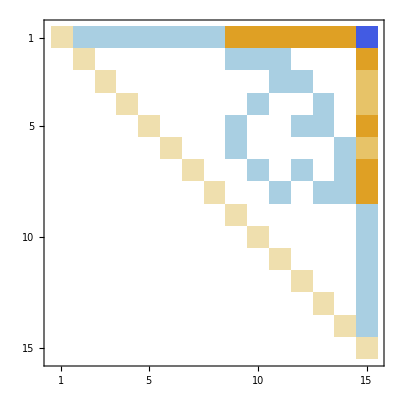

```mathematica
MatrixPower[Inverse[ZetaM],3]//MatrixPlot
```

```mathematica
MatrixPower[Inverse[ZetaM],15]//MatrixForm
```

(1 | -15 | -15 | -15 | -15 | -15 | -15 | -15 | 345 | 345 | 345 | 345 | 345 | 345 | -10695
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -15 | -15 | -15 | 0 | 0 | 0 | 345
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -15 | -15 | 0 | 0 | 225
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -15 | 0 | 0 | -15 | 0 | 225
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -15 | 0 | 0 | -15 | -15 | 0 | 345
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -15 | 0 | 0 | 0 | 0 | -15 | 225
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -15 | 0 | -15 | 0 | -15 | 345
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -15 | 0 | -15 | -15 | 345
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -15
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Subgraph
```

Subgraph

```mathematica
GraphZeta[g_]:=Block[{ordered=TopologicalSort[four]},
Table[If[ToString[i]==ToString[j]||EdgeQ[g,i->j],1,0],{i,ordered},{j,ordered}]
]
```

```mathematica
GraphZeta[four]//MatrixForm
```

(1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Inverse[GraphZeta[four]]//MatrixForm
```

(1 | -1 | -1 | -1 | 3 | -1 | -1 | 3 | -1 | 3 | -1 | 3 | 3 | 3 | -18
0 | 1 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 3
0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 3
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 2
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 1 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | -1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | -1 | -1 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)